```mathematica
p=0.09;
```

```mathematica
pde=D[g[x,t],t]-p*D[D[g[x,t],x],x]==0
DSolve[pde,g[x,t],{x,t}]
```

g^(0,1)[x,t]-0.09 g^(2,0)[x,t]==0

DSolve[g^(0,1)[x,t]-0.09 g^(2,0)[x,t]==0,g[x,t],{x,t}]

```mathematica
ClearAll[p]
term=(1-α)*p*gxn1+((-2*p)-α*(1-3*p))*gx+(p+α*(1-3*p))*gx1+α*p*gx2
```

(g-g1+g2/2-g3/6) p (1-α)+(g+2 g1+2 g2+(4 g3)/3) p α+g (-2 p-(1-3 p) α)+(g+g1+g2/2+g3/6) (p+(1-3 p) α)

```mathematica
gxn1=g-g1+g2/2-g3/6;
gx=g;
gx1=g+g1+g2/2+g3/6;
gx2=g+2*g1+2*g2+4/3*g3;
```

```mathematica
term
```

(g-g1+g2/2-g3/6) p (1-α)+(g+2 g1+2 g2+(4 g3)/3) p α+g (-2 p-(1-3 p) α)+(g+g1+g2/2+g3/6) (p+(1-3 p) α)

```mathematica
Simplify[term]
```

g2 p+g1 α+(g2 α)/2+(g3 α)/6+g3 p α

```mathematica
k[m-1]=g[m-2]*(α*(1-3*p)+p)+g[m-1]*(α*(1-3*p)+p)+g[m]*dn1+g[m+1]*dn2+g[m+2]*dn3;
k[m]=g[m-2]*(-g[m-2]*(1-2*p)-α*(1-3*p)+(1-2*p))+g[m-1]*(-g[m-2]*(1-2*p)-α*(1-3*p)+(1-2*p))+g[m]*d0+g[m+1]*dn1+g[m+2]*dn2+g[m+3]*dn3;
k[m+1]=g[m-2]*(-g[m-2]*p-α*p+p)+g[m-1]*(-g[m-2]*p-α*p+p)+g[m]*d1+g[m+1]*d0+g[m+2]*dn1+g[m+3]*dn2+g[m+4]*dn2+g[m+5]*dn3;
```

```mathematica
g[m-2]=0;
```

```mathematica
k[m-1]
```

(p+(1-3 p) α) g[-1+m]+(p+(1-3 p) α) g[m]+p α g[1+m]

```mathematica
k[m]
```

(1-2 p-(1-3 p) α) g[-1+m]+(1-2 p-(1-3 p) α) g[m]+(p+(1-3 p) α) g[1+m]+p α g[2+m]

```mathematica
k[m+1]
```

(p-p α) g[-1+m]+(p-p α) g[m]+(1-2 p-(1-3 p) α) g[1+m]+(p+(1-3 p) α) g[2+m]+p α g[3+m]+p α g[4+m]

```mathematica
(1-2 p-(1-3 p) α)+(1-2 p-(1-3 p) α)+(p+(1-3 p) α)+p α
```

2-3 p-(1-3 p) α+p α

```mathematica
dn3=g[m-2]*p;
dn2=g[m-2]*(1-2*p)+α*p;
dn1=α*(1-3*p)+p;
d0=-g[m-2]*(1-2*p)-α*(1-3*p)+(1-2*p);
d1=-g[m-2]*p-α*p+p;
```

```mathematica
x(y(1-x)+(1-y)x)+(1-x)(1-y)(1-x)
```

(1-x)^2 (1-y)+x (x (1-y)+(1-x) y)

```mathematica
mn1=(-1-p+α(1-3p))gmn1+(p+α(1-3p))gm+α*p*gm1;
m0=((1-2p)-α(1-3p))gmn1+(-2p-α(1-3p))gm+(p+α(1-3p))gm1+α*p*gm2;
m1=p(1-α)*gmn1+p(1-α)gm+(-2p-α(1-3p))gm1+(p+α(1-3p))gm2+α*p*gm3;
```

```mathematica
mn1=(-1-p+α(1-3p))gmn1+(p+α(1-3p))gm+α*p*gm1;
gmn1=g;
gm=g+g1+g2/2+g3/6;
gm1=g+2g1+2g2+8/6g3;
```

```mathematica
Simplify[mn1]
```

g (-1+(2-5 p) α)+1/6 (6 g1 (p+α-p α)+3 g2 (p+α+p α)+g3 (p+α+5 p α))

```mathematica
m0=((1-2p)-α(1-3p))kmn1+(-2p-α(1-3p))km+(p+α(1-3p))km1+α*p*km2;
kmn1=g-g1+g2/2-g3/6;
km=g;
km1=g+g1+g2/2+g3/6;
km2=g+2*g1+2*g2+4/3*g3;
```

```mathematica
Simplify[m0]
```

1/6 (3 g2-g3-3 g2 p+3 g3 p+2 g3 α+12 g2 p α+2 g3 p α-6 g1 (1-3 p-2 α+4 p α)+6 g (1-α+p (-3+4 α)))

```mathematica
Simplify[3 g2-g3-3 g2 p+3 g3 p+2 g3 α+12 g2 p α+2 g3 p α]
```

g3 (-1+2 α+p (3+2 α))+3 g2 (1+p (-1+4 α))

```mathematica
m1=p(1-α)*lmn1+p(1-α)lm+(-2p-α(1-3p))lm1+(p+α(1-3p))lm2+α*p*lm3;
lmn1=g-2g1+2g2-4/3*g3;
lm=g-g1+g2/2-g3/6;
lm1=g;
lm2=g+g1+g2/2+g3/6;
lm3=g+2*g1+2*g2+4/3*g3;
```

```mathematica
Simplify[m1]
```

g1 (2 p (-1+α)+α)+g (p-p α)+1/6 (3 g2 (6 p+α-4 p α)+g3 (-8 p+α+14 p α))

```mathematica
p=0.09;
a=0.00232053;
(1-3p-a(1-4p))a
p(1-a)a
```

0.00169054

0.000208363

```mathematica
pde=D[pg[x],x]+s*D[D[pg[x],x],x]==0
DSolve[pde,pg[x],{x}]
```

pg'[x]+s pg''[x]==0

{{pg[x]→-ⅇ^(-x/s) s C[1]+C[2]}}

```mathematica
ClearAll[a,p,α]

h=Function[{u},a-b*Exp[-u/(p/α+0.5)]][x]
```

a-b ⅇ^(-x/(0.5+p/α))

```mathematica
h{5}
```

{5 x^2}

```mathematica
Function[{u},a-b*Exp[-u/(p/α+0.5)]][3]
```

```mathematica
Sum[Function[{u},a-b*Exp[-u/(p/α+0.5)]][x],{x,0,4}]
```

5 a-b-b ⅇ^(-4/(0.5+p/α))-b ⅇ^(-3/(0.5+p/α))-b ⅇ^(-2/(0.5+p/α))-b ⅇ^(-1/(0.5+p/α))

```mathematica
ClearAll[a,b,p,α]
m=11;
pg[m-1]=α;
pg[m]=(1-3p-α(1-4p))α+Function[{u},a-b*Exp[-u/(p/α+0.5)]][m];
pg[m+1]=p(1-α)α+Function[{u},a-b*Exp[-u/(p/α+0.5)]][m+1];
For [i=m+2,i<301,i++,
pg[i]=Function[{u},a-b*Exp[-u/(p/α+0.5)]][i];
]
```

```mathematica
a=0;
α=0.00232053;
p=0.09;
```

```mathematica
Solve[Sum[pg[x],{x,m-1,300}]==1,b]
```

```mathematica
{{b->-0.03313650813342762}}
b=-0.03313650813342762;
```

{{b→-0.0331365}}

```mathematica
data1=Table[{i+1,pg[i]},{i,m-1,300}];
```

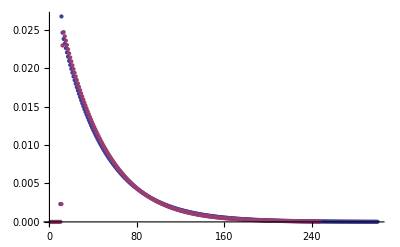

```mathematica
ListPlot[{data1,check3},PlotRange->Full]
```

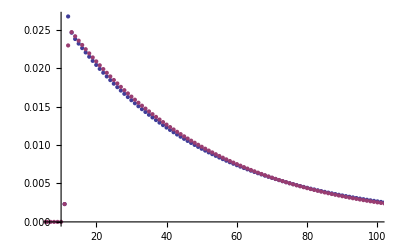

```mathematica
ListPlot[{data1,check3},PlotRange->{{7,100},Full}]
```

```mathematica
ClearAll[a,p,g,m]
m=11;
v1[m-3]=p*p;
v1[m-2]=p*(1-p);
v1[m-1]=1-p;
v[m-2]=p*p;
v[m-1]=p*(1-p);
v[m]=1-p;
v2[m-3]=a*p*p;
v2[m-2]=a*p*(1-p)+(1-a)*p*p;
v2[m-1]=a*(1-p)+(1-a)*p*(1-p);
v2[m]=(1-a)*(1-p);
```

```mathematica
g[m-1]=g[m-1]*(v1[m-3]*v2[m-3]+v1[m-2]*v2[m-2]+v1[m-1]*v2[m-1])+g[m]*(v[m-2]*v2[m-3]+v[m-1]*v2[m-2]+v[m]*v2[m-1])+g[m+1]*(v[m-1]*v2[m-3]+v[m]*v2[m-2])+g[m+2]*(v[m]*v2[m-3]);
g[m]=g[m-1]*(v1[m-3]*v2[m-2]+v1[m-2]*v2[m-1]+v1[m-1]*v2[m])+g[m]*(v[m-2]*v2[m-2]+v[m-1]*v2[m-1]+v[m]*v2[m])+
g[m+1]*(v[m-2]*v2[m-3]+v[m-1]*v2[m-2]+v[m]*v2[m-1])+g[m+2]*(v[m-1]*v2[m-3]+v[m]*v2[m-2])+g[m+3]*(v[m]*v2[m-3]);
g[m+1]=g[m-1]*(v1[m-3]*v2[m-1]+v1[m-2]*v2[m])+g[m]*(v[m-2]*v2[m-1]+v[m-1]*v2[m])+g[m+1]*(v[m-2]*v2[m-2]+v[m-1]*v2[m-1]+v[m]*v2[m])+g[m+2]*(v[m-2]*v2[m-3]+v[m-1]*v2[m-2]+v[m]*v2[m-1])+g[m+3]*(v[m-1]*v2[m-3]+v[m]*v2[m-2])+g[m+4]*(v[m]*v2[m-3]);
g[m+2]=g[m-1]*(v1[m-3]*v2[m])+g[m]*(v[m-2]*v2[m])+g[m+1]*(v[m-2]*v2[m-1]+v[m-1]*v2[m])+g[m+2]*(v[m-2]*v2[m-2]+v[m-1]*v2[m-1]+v[m]*v2[m])+g[m+3]*(v[m-2]*v2[m-3]+v[m-1]*v2[m-2]+v[m]*v2[m-1])+g[m+4]*(v[m-1]*v2[m-3]+v[m]*v2[m-2])+g[m+5]*(v[m]*v2[m-3]);
```

```mathematica
Simplify[g[m-1]*(v1[m-3]*v2[m-3]+v1[m-2]*v2[m-2]+v1[m-1]*v2[m-1])+g[m]*(v[m-2]*v2[m-3]+v[m-1]*v2[m-2]+v[m]*v2[m-1])+g[m+1]*(v[m-1]*v2[m-3]+v[m]*v2[m-2])+g[m+2]*(v[m]*v2[m-3])]
```

(-p (-1+2 p-2 p^2+p^3)+a (1-3 p+4 p^2-4 p^3+3 p^4)) g[-1+m]+(-p (-1+2 p-2 p^2+p^3)+a (1-3 p+4 p^2-4 p^3+3 p^4)) g[m]-(-1+p) p ((a (-1+p)^2+p) g[1+m]+a p g[2+m])

```mathematica
Simplify[g[m-1]*(v1[m-3]*v2[m-2]+v1[m-2]*v2[m-1]+v1[m-1]*v2[m])+g[m]*(v[m-2]*v2[m-2]+v[m-1]*v2[m-1]+v[m]*v2[m])+
g[m+1]*(v[m-2]*v2[m-3]+v[m-1]*v2[m-2]+v[m]*v2[m-1])+g[m+2]*(v[m-1]*v2[m-3]+v[m]*v2[m-2])+g[m+3]*(v[m]*v2[m-3])]
```

-(-1+2 p-2 p^2+2 p^3-2 p^4+a (1-3 p+4 p^2-4 p^3+3 p^4)) g[-1+m]-(-1+2 p-2 p^2+2 p^3-2 p^4+a (1-3 p+4 p^2-4 p^3+3 p^4)) g[m]+(-p (-1+2 p-2 p^2+p^3)+a (1-3 p+4 p^2-4 p^3+3 p^4)) g[1+m]-(-1+p) p (a (-1+p)^2+p) g[2+m]-a (-1+p) p^2 g[3+m]

```mathematica
Simplify[g[m-1]*(v1[m-3]*v2[m-1]+v1[m-2]*v2[m])+g[m]*(v[m-2]*v2[m-1]+v[m-1]*v2[m])+g[m+1]*(v[m-2]*v2[m-2]+v[m-1]*v2[m-1]+v[m]*v2[m])+g[m+2]*(v[m-2]*v2[m-3]+v[m-1]*v2[m-2]+v[m]*v2[m-1])+g[m+3]*(v[m-1]*v2[m-3]+v[m]*v2[m-2])+g[m+4]*(v[m]*v2[m-3])]
```

(-1+p) p (-1+a (-1+p)^2+p-p^2) g[-1+m]+(-1+p) p (-1+a (-1+p)^2+p-p^2) g[m]-(-1+2 p-2 p^2+2 p^3-2 p^4+a (1-3 p+4 p^2-4 p^3+3 p^4)) g[1+m]+(-p (-1+2 p-2 p^2+p^3)+a (1-3 p+4 p^2-4 p^3+3 p^4)) g[2+m]-(-1+p) p (a (-1+p)^2+p) g[3+m]-a (-1+p) p^2 g[4+m]

```mathematica
Simplify[g[m-1]*(v1[m-3]*v2[m])+g[m]*(v[m-2]*v2[m])+g[m+1]*(v[m-2]*v2[m-1]+v[m-1]*v2[m])+g[m+2]*(v[m-2]*v2[m-2]+v[m-1]*v2[m-1]+v[m]*v2[m])+g[m+3]*(v[m-2]*v2[m-3]+v[m-1]*v2[m-2]+v[m]*v2[m-1])+g[m+4]*(v[m-1]*v2[m-3]+v[m]*v2[m-2])+g[m+5]*(v[m]*v2[m-3])]
```

(-1+a) (-1+p) p^2 g[-1+m]+(-1+a) (-1+p) p^2 g[m]+(-1+p) p (-1+a (-1+p)^2+p-p^2) g[1+m]-(-1+2 p-2 p^2+2 p^3-2 p^4+a (1-3 p+4 p^2-4 p^3+3 p^4)) g[2+m]+(-p (-1+2 p-2 p^2+p^3)+a (1-3 p+4 p^2-4 p^3+3 p^4)) g[3+m]-(-1+p) p (a (-1+p)^2+p) g[4+m]-a (-1+p) p^2 g[5+m]

```mathematica
ClearAll[a,b,p,α]
m=11;

For [i=m+3,i<501,i++,
g[i]=Function[{u},a-b*Exp[-u/(p*(1-p)/α+0.5)]][i];
]

g[m-1]=α;
a=0;
d=0.02;
α=p(1-p)/(1/d-m-0.5);
p=0.1;
```

```mathematica
Solve[{x==g[m-1]*(v1[m-3]*v2[m-2]+v1[m-2]*v2[m-1]+v1[m-1]*v2[m])+x*(v[m-2]*v2[m-2]+v[m-1]*v2[m-1]+v[m]*v2[m])+
y*(v[m-2]*v2[m-3]+v[m-1]*v2[m-2]+v[m]*v2[m-1])+z*(v[m-1]*v2[m-3]+v[m]*v2[m-2])+g[m+3]*(v[m]*v2[m-3]),y==g[m-1]*(v1[m-3]*v2[m-1]+v1[m-2]*v2[m])+x*(v[m-2]*v2[m-1]+v[m-1]*v2[m])+y*(v[m-2]*v2[m-2]+v[m-1]*v2[m-1]+v[m]*v2[m])+z*(v[m-2]*v2[m-3]+v[m-1]*v2[m-2]+v[m]*v2[m-1])+g[m+3]*(v[m-1]*v2[m-3]+v[m]*v2[m-2])+g[m+4]*(v[m]*v2[m-3]),z==g[m-1]*(v1[m-3]*v2[m])+x*(v[m-2]*v2[m])+y*(v[m-2]*v2[m-1]+v[m-1]*v2[m])+z*(v[m-2]*v2[m-2]+v[m-1]*v2[m-1]+v[m]*v2[m])+g[m+3]*(v[m-2]*v2[m-3]+v[m-1]*v2[m-2]+v[m]*v2[m-1])+g[m+4]*(v[m-1]*v2[m-3]+v[m]*v2[m-2])+g[m+5]*(v[m]*v2[m-3])},{x,y,z}]
```

{{x→0.0155936-0.182447 b,y→0.0106365-0.348472 b,z→0.00567936-0.514338 b}}

```mathematica
g[m]=0.015593600042836966-0.18244724257186432 b
g[m+1]=0.010636470001063589-0.34847213178895103 b
g[m+2]=0.005679363336147401-0.5143379006722029 b
```

0.0155936-0.182447 b

0.0106365-0.348472 b

0.00567936-0.514338 b

```mathematica
Solve[Sum[g[x],{x,m-1,500}]==1,b]
```

{{b→-0.0337285}}

```mathematica
b=-0.03372850189809957;
```

```mathematica
data4=Table[{i+1,g[i]},{i,m-1,300}];
```

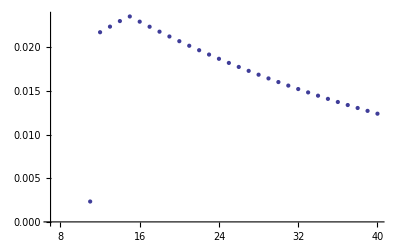

```mathematica
ListPlot[{data4},PlotRange->{{7,40},Full}]
```

```mathematica
ClearAll[a,b,p,α]
m=11;

For [i=m+3,i<1001,i++,
g[i]=Function[{u},a-b*Exp[-u/(p*(1-p)/α+0.5)]][i];
]

g[m-1]=α;
a=0;
d=0.02;
α=p(1-p)/(1/d-m-0.5);
α=0.00207199;
p=0.1;
```

```mathematica
g[m+2]=g[m-1]*(v1[m-3]*v2[m])+Function[{u},a-b*Exp[-u/(p*(1-p)/α+0.5)]][m+2];
```

```mathematica
g[m+2]
```

0.0000186479-0.743876 b

```mathematica
Solve[{x==g[m-1]*(v1[m-3]*v2[m-2]+v1[m-2]*v2[m-1]+v1[m-1]*v2[m])+x*(v[m-2]*v2[m-2]+v[m-1]*v2[m-1]+v[m]*v2[m])+
y*(v[m-2]*v2[m-3]+v[m-1]*v2[m-2]+v[m]*v2[m-1])+g[m+2]*(v[m-1]*v2[m-3]+v[m]*v2[m-2])+g[m+3]*(v[m]*v2[m-3]),y==g[m-1]*(v1[m-3]*v2[m-1]+v1[m-2]*v2[m])+x*(v[m-2]*v2[m-1]+v[m-1]*v2[m])+y*(v[m-2]*v2[m-2]+v[m-1]*v2[m-1]+v[m]*v2[m])+g[m+2]*(v[m-2]*v2[m-3]+v[m-1]*v2[m-2]+v[m]*v2[m-1])+g[m+3]*(v[m-1]*v2[m-3]+v[m]*v2[m-2])+g[m+4]*(v[m]*v2[m-3])},{x,y}]
```

{{x→0.0122329-0.255953 b,y→0.00645269-0.486415 b}}

```mathematica
g[m]=0.012232924570161258-0.2559528892604022 b
g[m+1]=0.006452693988587499-0.4864145953325545 b
```

0.0122329-0.255953 b

0.00645269-0.486415 b

```mathematica
Solve[Sum[g[x],{x,m-1,200}]==1,b]
```

{{b→-0.02937}}

```mathematica
b=-0.029370034884501735;
```

```mathematica
data6=Table[{i+1,g[i]},{i,m-1,300}];
```

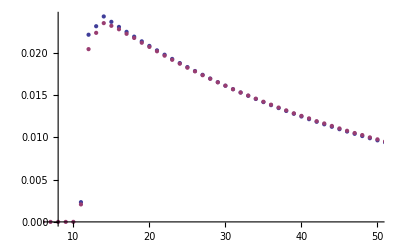

```mathematica
ListPlot[{data5,gap8},PlotRange->{{7,50},Full}]
```

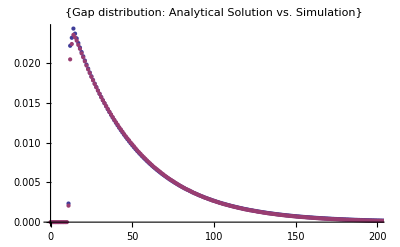

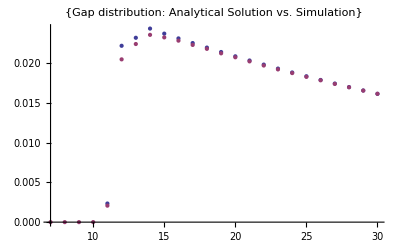

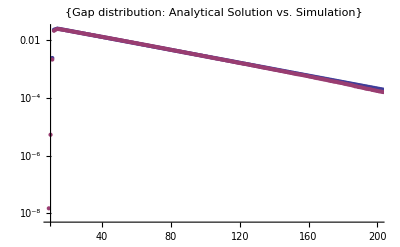

```mathematica
ListPlot[{data5,gap8},PlotRange->{{0,200},Full},PlotLabel->{"Gap distribution: Analytical Solution vs. Simulation"}]
ListPlot[{data5,gap8},PlotRange->{{7,30},Full},PlotLabel->{"Gap distribution: Analytical Solution vs. Simulation"}]
ListLogPlot[{data5,gap8},PlotRange->{{10,200},Full},PlotLabel->{"Gap distribution: Analytical Solution vs. Simulation"}]
```

```mathematica
gap8[[12]]
```

{11,0.00207199}

```mathematica
α
```

0.00233766

```mathematica
0.00207199
```